```mathematica
f[{p_,o_}]:=dis[[p,o]]
Life[alloc_]:=Total[f/@alloc]
Wait[w_,p_,alloc_]:=Total[w⟦Complement[p,alloc[[All,1]]]⟧]
Goal[w_,p_,alloc_]:=(Wait[w,p,alloc]+Life[alloc])/n
Goal[alloc_]:=Goal[w,p,alloc]
NormlizedGoal[w_,p_,alloc_]:=(Goal[w,p,alloc]-Total[w[[p]]])/n
FilterAllocation[w_,alloc_]:=MapIndexed[If[
#2[[1]]<=w[[#1[[1]]]]&&f[#1]>w[[#2[[1]]]],#1,Nothing]&,alloc]
RandomAlloc[w_,p_,o_]:=FilterAllocation[w,{RandomSample[p][[;;Min[m,n]]],RandomSample[o][[;;Min[m,n]]]}ᵀ]
SampleGoal[w_,p_,o_]:=Goal[w,p,RandomAlloc[w,p,o]]
NormalEdgeForm[ed_]:=(ed/.{Subscript[_, i_]->i})/.DirectedEdge->List
Zero[a_,b_]:=ConstantArray[Infinity,{a,b}]
PlaceAtLast[item_, list_, last_]:=
Module[{l},
l=FindPosition[list,last];
If[Length[l]==0,Return[list]];
Return[ReplacePart[list,Last[l]->item]]
]
FindPosition[alloc_,last_]:=Flatten[Position[alloc[[;;Min[last,Length[alloc]]]],0]]
```

```mathematica
var[i_,j_, t_] := Symbol["x"<>ToString@i<>"d" <>ToString@j <> "d" <> ToString@t];
waitConstr[w_, i_] :=  Table[Symbol["x"<>ToString@i<>"d" <>ToString@j <> "d" <> ToString@t] == 0, {j, m}, {t, w+1, T}] // Flatten;
SplitRes[s_]:= ToString@s// StringSplit[#, "x"]& // StringSplit[#, "d"]& //ToExpression// Flatten;
ExtractAllocation[res_]:=SortBy[SplitRes[#[[1]]] & /@ Select[res, (#[[2]] == 1&)], Last];
```

```mathematica
Sim[]:=Module[{},
n=25;
m=8;
λ=Ceiling[m/2]+1;
p=Range[n];
o=Range[m];
{patients,organs}={Table[Subscript[pt, i],{i,n}],Table[Subscript[or, i],{i,m}]};
w=RandomVariate[PoissonDistribution[λ],n];pZ=RandomVariate[NormalDistribution[0,10],n];oZ=RandomVariate[NormalDistribution[0,10],m];dis=5 Ramp[DistanceMatrix[pZ,oZ]-12];

alc=ConstantArray[0,Min[m,n]];
{pRm,oRm}={Range[n],Range[m]};
While[(Length[oRm]>0)&&(Length[pRm]>0),
adj=Transpose[Join[(Join[ConstantArray[∞,Length[oRm]],#1]&)/@Transpose[dis[[pRm,oRm]]],Zero[Length[pRm],Length[oRm]+Length[pRm]]]/.{0.->∞}];g=WeightedAdjacencyGraph[Join[organs[[oRm]],patients[[pRm]]],adj];
If[Length[g//EdgeList]==0,Break[];Print["Breaking"];];
mm=NormalEdgeForm/@FindMaximumFlow[g,patients[[pRm]],organs[[oRm]],"EdgeList",VertexCapacity->ConstantArray[1,Length[oRm]+Length[pRm]]];wait=w⟦mm⟦All,1⟧⟧;gains=f/@mm-wait;next=Ordering[gains,-1][[1]];
alc=PlaceAtLast[mm[[next]],alc,w[[next]]];
oRm=oRm/.{mm[[next]][[2]]->Nothing};
pRm=pRm/.{mm[[next]][[1]]->Nothing};
];
greedy=Goal[alc/.{0->Nothing}];

T = Min[m, n];

obj1 = Table[-dis[[i,j]]*var[i,j,t], {i,  n}, {j,  m}, {t, T}] // Flatten // Total;
obj2 = Table[-w[[i]] * (1 - (Table[var[i,j,t], {j, m},{t, T}] // Flatten // Total )), {i, n}]  // Total;
obj = obj1 + obj2;
constr = Table[(Flatten[Table[var[i,j,t], {j, m},{t, T}] ] // Total) <= 1, {i, n}];
constr2 = Table[( Flatten[Table[var[i,j,t], {i, n}, {t, T}]] //Total) <= 1, {j, m}];
constr3 = Table[ (Flatten[Table[var[i,j,t], {i, n}, {j, m}]] //Total)<= 1, {t, T}];
constr4 = Table[var[i,j,t] >= 0, {i, n}, {j, m}, {t, T}] // Flatten;
constr5 = waitConstr[#[[1]], #[[2]]]&/@Transpose[{w, p}] // Flatten;
res = LinearOptimization[obj1+obj2, constr~Join~constr2~Join~constr3~Join~constr4~Join~constr5, Table[var[i,j,t]∈ Integers, {i, n}, {j, m}, {t, T}]//Flatten];
opt=-(obj/.res)/ n;
rdn=Max@Table[SampleGoal[w,p,o],n+m];
Return[opt/{greedy,rdn}]
]
```

```mathematica
res=ResourceFunction["MonitorProgress"]@Table[Sim[],1000]ᵀ;
```

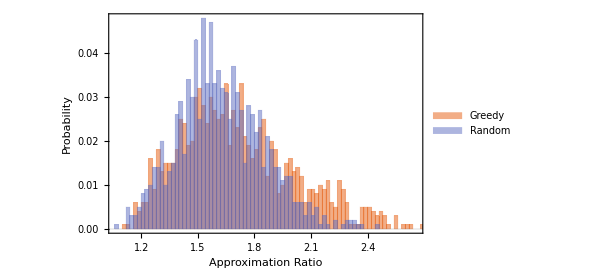

```mathematica
Histogram[res,100,"Probability",Frame->True,FrameLabel->{"Approximation Ratio","Probability"},LabelStyle->{FontSize->18,FontColor->Black,FontFamily->"CMU Sans Serif"},PlotTheme->"Scientific",ChartLegends->Placed[{"Greedy","Random"},{.7,.8}]]
```